Realizaciones estocásticas

Estudiaremos el modelo:   x_(n+1)= 1+2a|x_n|- by_n ; y_(n+1)=x_n

número de iteraciones

```mathematica
NN=32000;
```

parámetros de la recurrencia

Caso Devaney

Para obtener el caso determinista cambiar a e = 0.

```mathematica
a=1/2;b=1; noiseLevel=0.001; e=1;
```

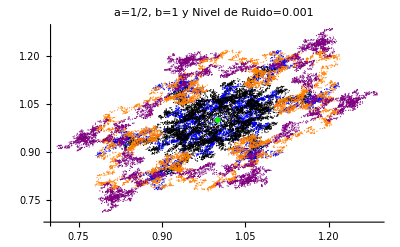

```mathematica
Xf=Array[nada,NN]; Yf=Array[nada,NN];Epsif=ConstantArray[0,{2,NN}];
Xf[[1]]=1; Yf[[1]]=1;
For[i=1,i<=NN,i++,SeedRandom[4022+i];
Epsif[[1,i]]=RandomVariate[NormalDistribution[0,noiseLevel]];
SeedRandom[i+NN];Epsif[[2,i]]=RandomVariate[NormalDistribution[0,noiseLevel]]];
For[i=1,i<NN,i++,Xf[[i+1]]=1-b*Yf[[i]]+2*a*Abs[Xf[[i]]]+e*Epsif[[1,i]]; Yf[[i+1]]=Xf[[i]]+e*Epsif[[2,i]]];
Xf2=Xf[[1;;NN/4]];Yf2=Yf[[1;;NN/4]];
Xf4=Xf[[NN/4;;NN/2]];Yf4=Yf[[NN/4;;NN/2]];
Xf6=Xf[[NN/2;;3*NN/4]];Yf6=Yf[[NN/2;;3*NN/4]];
Xf8=Xf[[3*NN/4;;NN]];Yf8=Yf[[3*NN/4;;NN]];
ListPlot[{Transpose[{Xf2,Yf2}],Transpose[{Xf4,Yf4}], Transpose[{Xf6,Yf6}],Transpose[{Xf8,Yf8}]},FrameLabel->{"x[n]","y[n]"},PlotLabel->"a=1/2, b=1 y Nivel de Ruido=0.001",PlotStyle->{Directive[PointSize[0.002],Blue],Directive[PointSize[0.002],Black],Directive[PointSize[0.002],Orange],Directive[PointSize[0.002],Purple],Directive[PointSize[0.002],Red]},Epilog->{Green,PointSize[0.01],Point[{Xf2[[1]],Yf2[[1]]}]},PlotRange->Full]
```

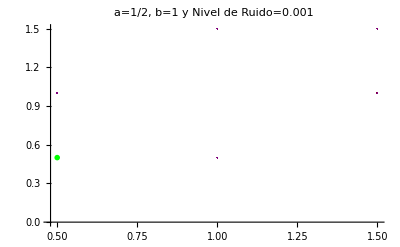

```mathematica
Xint=Array[nada,NN]; Yint=Array[nada,NN]; Epsiint=ConstantArray[0,{2,NN}];
Xint[[1]]=0.5; Yint[[1]]=0.5;
For[i=1,i<=NN,i++,SeedRandom[4022+i];
Epsiint[[1,i]]=RandomVariate[NormalDistribution[0,noiseLevel]];
SeedRandom[i+NN];Epsiint[[2,i]]=RandomVariate[NormalDistribution[0,noiseLevel]]];
For[i=1,i<NN,i++,Xint[[i+1]]=1-b*Yint[[i]]+Abs[Xint[[i]]]+e*Epsiint[[1,i]]; Yint[[i+1]]=Xint[[i]]+e*Epsiint[[2,i]]];
Xint2=Xint[[1;;NN/4]];Yint2=Yint[[1;;NN/4]];
Xint4=Xint[[NN/4;;NN/2]];Yint4=Yint[[NN/4;;NN/2]];
Xint6=Xint[[NN/2;;3*NN/4]];Yint6=Yint[[NN/2;;3*NN/4]];
Xint8=Xint[[3*NN/4;;NN]];Yint8=Yint[[3*NN/4;;NN]];
ListPlot[{Transpose[{Xint2,Yint2}],Transpose[{Xint4,Yint4}],Transpose[{Xint6,Yint6}],Transpose[{Xint8,Yint8}]},FrameLabel->{"x[n]","y[n]"},PlotLabel->"a=1/2, b=1 y Nivel de Ruido=0.001",PlotStyle->{Directive[PointSize[0.002],Blue],Directive[PointSize[0.002],Black],Directive[PointSize[0.002],Orange],Directive[PointSize[0.002],Purple],Directive[PointSize[0.002],Red]},Epilog->{Green,PointSize[0.01],Point[{Xint2[[1]],Yint2[[1]]}]},PlotRange->Full]
```

```mathematica
Xexa=Array[nada,NN]; Yexa=Array[nada,NN]; Epsiexa=ConstantArray[0,{2,NN}];
Xexa[[1]]=5; Yexa[[1]]=3;
For[i=1,i<=NN,i++,SeedRandom[4022+i];
Epsiexa[[1,i]]=RandomVariate[NormalDistribution[0,noiseLevel]];
SeedRandom[i+NN];Epsiexa[[2,i]]=RandomVariate[NormalDistribution[0,noiseLevel]]];
For[i=1,i<NN,i++,Xexa[[i+1]]=1-b*Yexa[[i]]+2*a*Abs[Xexa[[i]]]+e*Epsiexa[[1,i]]; Yexa[[i+1]]=Xexa[[i]]+e*Epsiexa[[2,i]]];
Xexa2=Xexa[[1;;NN/4]];Yexa2=Yexa[[1;;NN/4]];
Xexa4=Xexa[[NN/4;;NN/2]];Yexa4=Yexa[[NN/4;;NN/2]];
Xexa6=Xexa[[NN/2;;3*NN/4]];Yexa6=Yexa[[NN/2;;3*NN/4]];
Xexa8=Xexa[[3*NN/4;;NN]];Yexa8=Yexa[[3*NN/4;;NN]];
ListPlot[{Transpose[{Xexa2,Yexa2}],Transpose[{Xexa4,Yexa4}],Transpose[{Xexa6,Yexa6}],Transpose[{Xexa8,Yexa8}]},FrameLabel->{"x[n]","y[n]"},PlotLabel->"a=1/2, b=1 y Nivel de Ruido=0.001",PlotStyle->{Directive[PointSize[0.002],Blue],Directive[PointSize[0.002],Black],Directive[PointSize[0.002],Orange],Directive[PointSize[0.002],Purple],Directive[PointSize[0.002],Red]},Epilog->{Green,PointSize[0.01],Point[{Xexa2[[1]],Yexa2[[1]]}]},PlotRange->Full]
```

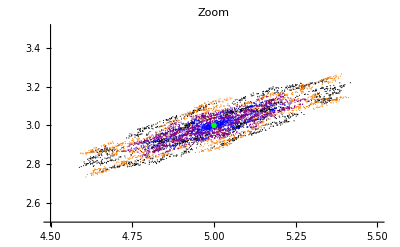

```mathematica
ListPlot[{Transpose[{Xexa2,Yexa2}],Transpose[{Xexa4,Yexa4}],Transpose[{Xexa6,Yexa6}],Transpose[{Xexa8,Yexa8}]},FrameLabel->{"x[n]","y[n]"},PlotLabel->"Zoom",PlotStyle->{Directive[PointSize[0.002],Blue],Directive[PointSize[0.002],Black],Directive[PointSize[0.002],Orange],Directive[PointSize[0.002],Purple],Directive[PointSize[0.002],Red]},Epilog->{Green,PointSize[0.01],Point[{Xexa2[[1]],Yexa2[[1]]}]},PlotRange->{{4.5,5.5},{2.5,3.5}}]
```

```mathematica
Xext=Array[nada,NN]; Yext=Array[nada,NN];Epsiext=ConstantArray[0,{2,NN}];
Xext[[1]]=2.1; Yext[[1]]=2.1;
For[i=1,i<=NN,i++,SeedRandom[4022+i];
Epsiext[[1,i]]=RandomVariate[NormalDistribution[0,noiseLevel]];
SeedRandom[i+NN];Epsiext[[2,i]]=RandomVariate[NormalDistribution[0,noiseLevel]]];
For[i=1,i<NN,i++,Xext[[i+1]]=1-b*Yext[[i]]+2*a*Abs[Xext[[i]]]+e*Epsiext[[1,i]]; Yext[[i+1]]=Xext[[i]]+e*Epsiext[[2,i]]];
Xext2=Xext[[1;;NN/4]];Yext2=Yext[[1;;NN/4]];
Xext4=Xext[[NN/4;;NN/2]];Yext4=Yext[[NN/4;;NN/2]];
Xext6=Xext[[NN/2;;3*NN/4]];Yext6=Yext[[NN/2;;3*NN/4]];
Xext8=Xext[[3*NN/4;;NN]];Yext8=Yext[[3*NN/4;;NN]];
ListPlot[{Transpose[{Xext2,Yext2}],Transpose[{Xext4,Yext4}],Transpose[{Xext6,Yext6}],Transpose[{Xext8,Yext8}]},FrameLabel->{"x[n]","y[n]"},PlotLabel->"a=1/2, b=1 y Nivel de Ruido=0.001",PlotStyle->{Directive[PointSize[0.002],Blue],Directive[PointSize[0.002],Black],Directive[PointSize[0.002],Orange],Directive[PointSize[0.002],Purple],Directive[PointSize[0.002],Red]},Epilog->{Green,PointSize[0.01],Point[{Xext2[[1]],Yext2[[1]]}]},PlotRange->Full]
```

Caso elipses

```mathematica
a=0.999/2;b=1;
Xf09=Array[nada,NN]; Yf09=Array[nada,NN];
Epsif09=ConstantArray[0,{2,NN}];
Xf09[[1]]=1; Yf09[[1]]=1;
For[i=1,i<=NN,i++,SeedRandom[4022+i];
Epsif09[[1,i]]=RandomVariate[NormalDistribution[0,noiseLevel]];
SeedRandom[i+NN];Epsif09[[2,i]]=RandomVariate[NormalDistribution[0,noiseLevel]]];
For[i=1,i<NN,i++,Xf09[[i+1]]=1-b*Yf09[[i]]+2*a*Abs[Xf09[[i]]]+e*Epsif09[[1,i]]; Yf09[[i+1]]=Xf09[[i]]+e*Epsif09[[2,i]]];
Xf092=Xf09[[1;;NN/4]];Yf092=Yf09[[1;;NN/4]];
Xf094=Xf09[[NN/4;;NN/2]];Yf094=Yf09[[NN/4;;NN/2]];
Xf096=Xf09[[NN/2;;3*NN/4]];Yf096=Yf09[[NN/2;;3*NN/4]];
Xf098=Xf09[[3*NN/4;;NN]];Yf098=Yf09[[3*NN/4;;NN]];
ListPlot[{Transpose[{Xf092,Yf092}],Transpose[{Xf094,Yf094}],Transpose[{Xf096,Yf096}],Transpose[{Xf098,Yf098}]},FrameLabel->{"x[n]","y[n]"},PlotLabel->"2a=0.999, b=1 y Nivel de Ruido=0.001",PlotStyle->{Directive[PointSize[0.002],Blue],Directive[PointSize[0.002],Black],Directive[PointSize[0.002],Orange],Directive[PointSize[0.002],Purple],Directive[PointSize[0.002],Red]},Epilog->{Green,PointSize[0.01],Point[{Xf092[[1]],Yf092[[1]]}]},PlotRange->Full]
```

```mathematica
Xint09=Array[nada,NN]; Yint09=Array[nada,NN];
Epsiint09=ConstantArray[0,{2,NN}];
Xint09[[1]]=0.5; Yint09[[1]]=0.5;
For[i=1,i<=NN,i++,SeedRandom[4022+i];
Epsiint09[[1,i]]=RandomVariate[NormalDistribution[0,noiseLevel]];
SeedRandom[i+NN];Epsiint09[[2,i]]=RandomVariate[NormalDistribution[0,noiseLevel]]];
For[i=1,i<NN,i++,Xint09[[i+1]]=1-b*Yint09[[i]]+2*a*Abs[Xint09[[i]]]+e*Epsiint09[[1,i]]; Yint09[[i+1]]=Xint09[[i]]+e*Epsiint09[[2,i]]];
Xint092=Xint09[[1;;NN/4]];Yint092=Yint09[[1;;NN/4]];
Xint094=Xint09[[NN/4;;NN/2]];Yint094=Yint09[[NN/4;;NN/2]];
Xint096=Xint09[[NN/2;;3*NN/4]];Yint096=Yint09[[NN/2;;3*NN/4]];
Xint098=Xint09[[3*NN/4;;NN]];Yint098=Yint09[[3*NN/4;;NN]];
ListPlot[{Transpose[{Xint092,Yint092}],Transpose[{Xint094,Yint094}],Transpose[{Xint096,Yint096}],Transpose[{Xint098,Yint098}],SOLa09b11},FrameLabel->{"x[n]","y[n]"},PlotLabel->"2a=0.999, b=1 y Nivel de Ruido=0.001",PlotStyle->{Directive[PointSize[0.002],Blue],Directive[PointSize[0.002],Black],Directive[PointSize[0.002],Orange],Directive[PointSize[0.002],Purple],Directive[PointSize[0.002],Red]},Epilog->{Green,PointSize[0.01],Point[{Xint092[[1]],Yint092[[1]]}]},PlotRange->Full]
```

```mathematica
Xext09=Array[nada,NN]; Yext09=Array[nada,NN];
Epsiext09=ConstantArray[0,{2,NN}];
Xext09[[1]]=2.1; Yext09[[1]]=2.1;
For[i=1,i<=NN,i++,SeedRandom[4022+i];
Epsiext09[[1,i]]=RandomVariate[NormalDistribution[0,noiseLevel]];
SeedRandom[i+NN];Epsiext09[[2,i]]=RandomVariate[NormalDistribution[0,noiseLevel]]];
For[i=1,i<NN,i++,Xext09[[i+1]]=1-b*Yext09[[i]]+2*a*Abs[Xext09[[i]]]+e*Epsiext09[[1,i]]; Yext09[[i+1]]=Xext09[[i]]+e*Epsiext09[[2,i]]];
Xext092=Xext09[[1;;NN/4]];Yext092=Yext09[[1;;NN/4]];
Xext094=Xext09[[NN/4;;NN/2]];Yext094=Yext09[[NN/4;;NN/2]];
Xext096=Xext09[[NN/2;;3*NN/4]];Yext096=Yext09[[NN/2;;3*NN/4]];
Xext098=Xext09[[3*NN/4;;NN]];Yext098=Yext09[[3*NN/4;;NN]];
ListPlot[{Transpose[{Xext092,Yext092}],Transpose[{Xext094,Yext094}],Transpose[{Xext096,Yext096}],Transpose[{Xext098,Yext098}]},FrameLabel->{"x[n]","y[n]"},PlotLabel->"2a=0.999, b=1 y Nivel de Ruido=0.001",PlotStyle->{Directive[PointSize[0.002],Blue],Directive[PointSize[0.002],Black],Directive[PointSize[0.002],Orange],Directive[PointSize[0.002],Purple],Directive[PointSize[0.002],Red]},Epilog->{Green,PointSize[0.01],Point[{Xext092[[1]],Yext092[[1]]}]},PlotRange->Full]
```

```mathematica
Xexa09=Array[nada,NN]; Yexa09=Array[nada,NN];
Epsiexa09=ConstantArray[0,{2,NN}];
Xexa09[[1]]=3; Yexa09[[1]]=5.3;
For[i=1,i<=NN,i++,SeedRandom[4022+i];
Epsiexa09[[1,i]]=RandomVariate[NormalDistribution[0,noiseLevel]];
SeedRandom[i+NN];Epsiexa09[[2,i]]=RandomVariate[NormalDistribution[0,noiseLevel]]];
For[i=1,i<NN,i++,Xexa09[[i+1]]=1-b*Yexa09[[i]]+2*a*Abs[Xexa09[[i]]]+e*Epsiexa09[[1,i]]; Yexa09[[i+1]]=Xexa09[[i]]+e*Epsiexa09[[2,i]]];
Xexa092=Xexa09[[1;;NN/4]];Yexa092=Yexa09[[1;;NN/4]];
Xexa094=Xexa09[[NN/4;;NN/2]];Yexa094=Yexa09[[NN/4;;NN/2]];
Xexa096=Xexa09[[NN/2;;3*NN/4]];Yexa096=Yexa09[[NN/2;;3*NN/4]];
Xexa098=Xexa09[[3*NN/4;;NN]];Yexa098=Yexa09[[3*NN/4;;NN]];
ListPlot[{Transpose[{Xexa092,Yexa092}],Transpose[{Xexa094,Yexa094}],Transpose[{Xexa096,Yexa096}],Transpose[{Xexa098,Yexa098}],SOLa09b15},FrameLabel->{"x[n]","y[n]"},PlotLabel->"2a=0.999, b=1 y Nivel de Ruido=0.001",PlotStyle->{Directive[PointSize[0.002],Blue],Directive[PointSize[0.002],Black],Directive[PointSize[0.002],Orange],Directive[PointSize[0.002],Purple],Directive[PointSize[0.002],Red]},Epilog->{Green,PointSize[0.01],Point[{Xexa092[[1]],Yexa092[[1]]}]},PlotRange->Full]
```

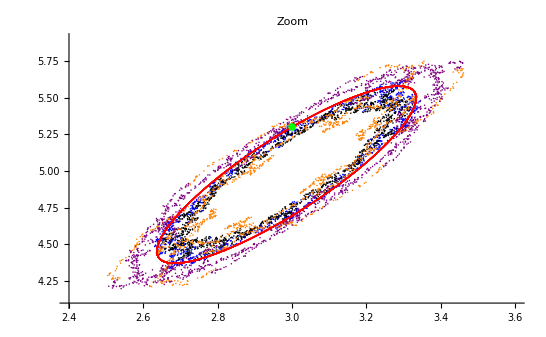

```mathematica
ListPlot[{Transpose[{Xexa092,Yexa092}],Transpose[{Xexa094,Yexa094}],Transpose[{Xexa096,Yexa096}],Transpose[{Xexa098,Yexa098}],SOLa09b15},FrameLabel->{"x[n]","y[n]"},PlotLabel->"Zoom",PlotStyle->{Directive[PointSize[0.002],Blue],Directive[PointSize[0.002],Black],Directive[PointSize[0.002],Orange],Directive[PointSize[0.002],Purple],Directive[PointSize[0.002],Red]},Epilog->{Green,PointSize[0.01],Point[{Xexa092[[1]],Yexa092[[1]]}]},PlotRange->{{2.4,3.6},{4.1,5.9}}]
```